## Tools

```mathematica
(*cl[d_,l_]:=(Sqrt[π]Gamma[l+1]Gamma[(d-2)/2])/(2^(l+1) Gamma[l+(d-1)/2]);(*some other normalization term*)(*d-dim Partial Wave integrand {t,4,∞}*)*)
```

```mathematica
Clear[PolQ, PolQDer, z0t,z0u,tt,uu,discZ];
PolQ[J_, d_, z_]:=(4/Pi)(Sqrt[Pi]Gamma[J+1]Gamma[(d-2)/2])/(2^(J+1)Gamma[J+(d-1)/2] z^(J+1))Hypergeometric2F1[(J+1)/2,(J+2)/2, J+(d-1)/2,1/z^2](*cl[d,l]/x^(l+d-3) Hypergeometric2F1[(l+d-3)/2,(l+d-2)/2,l+(d-1)/2,1/x^2]/.x->z/.l->J*);
PolQDer[J_,d_,z_,n_]:=(D[PolQ[J,d,zz],{zz,n}]/.zz->z);
z0t[s_]:= (s+4)/(s-4);
z0u[s_]:= (s+4)/(4-s);
tt[s_,z_]:=((4-s)/2) (1-z);
uu[s_,z_]:=((4-s)/2 )(1+z);
discZ[expr_,s_,z_,eps_:10^-12]:= (expr[Re[s],z+eps I]-expr[Re[s],z-eps I])/(2I)
```

```mathematica
Clear[iQInfinity12,tail]
iQInfinity12[start_, J_, d_]=Integrate[PolQ[J,d,z] 1/z^(1/2), {z, start, Infinity}, GenerateConditions->False]
tail[amplitudeT_, s_, J_, d_, start_]:= Module[{zvals, yvals, coeff12},
								zvals = Abs[start[s]]*{100000,1000000, 10000000};
								yvals=amplitudeT[s,#]&/@zvals;
								coeff12=Mean[yvals*zvals^(1/2)];
								iQInfinity12[50000Abs[start[s]], J, d]coeff12]
```

1/(√π)2^-J (1/start^2)^(1/4+J/2) Gamma[1/4+J/2] Gamma[1+J] HypergeometricPFQRegularized[{1/4 (1+2 J),(1+J)/2,(2+J)/2},{1/4 (5+2 J),3/2+J},1/start^2]

```mathematica
2^(-2-J) √π (1/start^2)^(1/4+J/2) Gamma[-1+d/2] Gamma[1/4+J/2] Gamma[1+J] HypergeometricPFQRegularized[{1/4 (1+2 J),(1+J)/2,(2+J)/2},{1/4 (5+2 J),1/2 (-1+d)+J},1/start^2]/.start->z//FullSimplify
```

2^(-2-J) √π (1/z^2)^(1/4+J/2) Gamma[1/4+J/2] Gamma[1+J] HypergeometricPFQRegularized[{1/4 (1+2 J),(1+J)/2,(2+J)/2},{1/4 (5+2 J),3/2+J},1/z^2]

```mathematica
Clear[MyNIntegrateFaster];
MyNIntegrateFaster[expr_,{x_,a_,b_},p_]:=Module[{temp=expr},(*Print["integrate..."];*)temp=SetPrecision[temp,8*p];
temp=NIntegrate[temp,{x,a,b},Method->"GaussKronrodRule",WorkingPrecision->4*p,PrecisionGoal->p,AccuracyGoal->p,MaxRecursion->100];
temp=SetPrecision[temp,p];
Return[temp];];
```

## Building the discontinuity (s real!!!)

```mathematica
Clear[t,u, rho, rhoT,rhoZ]
rho[s_,sigma_:20/3]:=(Sqrt[sigma-4]-Sqrt[4-s])/(Sqrt[sigma-4]+Sqrt[4-s])
rhoZ[s_,z_]:=rho[tt[s,z]];
rhoT[t_,sigma_:20/3]:=(2 Sqrt[t-4] Sqrt[sigma-4])/(t+sigma-8)
```

```mathematica
Clear[It,ItEps,error]
It[J_,s_]:=MyNIntegrateFaster[rhoT[tt[s,z]]PolQ[J,4,z],{z,z0t[s],Infinity},16]
ItEps[J_,s_,eps_:10^-12]:=MyNIntegrateFaster[discZ[rhoZ,s,z, eps]PolQ[J,4,z],{z,z0t[s],Infinity},16]
error[J_,s_,eps_:10^-12]:=Abs[(It[J,s]-ItEps[J,s,eps])/(It[J,s]+ItEps[J,s,eps])]
```

```mathematica
DiscData2=ParallelTable[{a,error[2,s+10^(-a+1), 10^-a]},{s,5,95,10},{a,0,16}];
DiscData20=ParallelTable[{a,error[20,s+10^(-a+1), 10^-a]},{s,5,95,10},{a,0,16}];
DiscData2I=ParallelTable[{a,error[2+I,s+10^(-a+1), 10^-a]},{s,5,95,10},{a,0,16}];
```

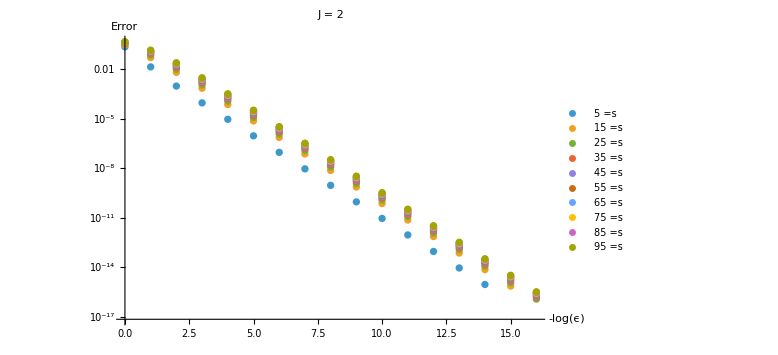

```mathematica
ListLogPlot[DiscData2,PlotLabel->Style["J = 2",16,Bold],AxesLabel->{Style["-log(ϵ)",14],Style["Error",14]},PlotLegends->"=s"Range[5,95,10],ImageSize->Large]
```

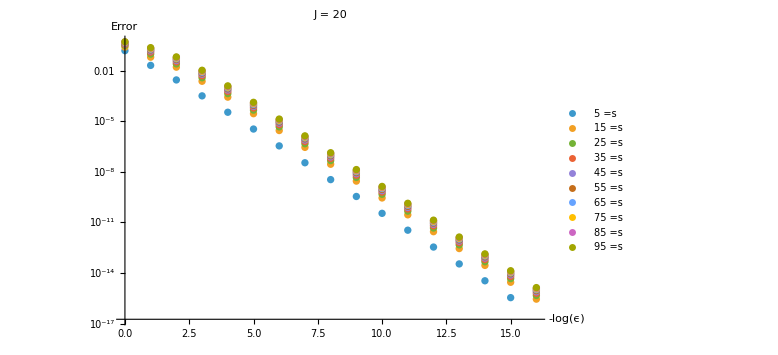

```mathematica
ListLogPlot[DiscData20,PlotLabel->Style["J = 20",16,Bold],AxesLabel->{Style["-log(ϵ)",14],Style["Error",14]},PlotLegends->"=s"Range[5,95,10],ImageSize->Large]
```

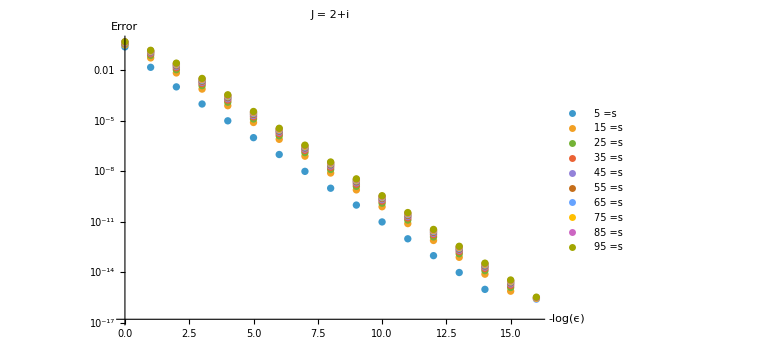

```mathematica
ListLogPlot[DiscData2I,PlotLabel->Style["J = 2+i",16,Bold],AxesLabel->{Style["-log(ϵ)",14],Style["Error",14]},PlotLegends->"=s"Range[5,95,10],ImageSize->Large]
```

## Computing the tale

```mathematica
pathFile="/Users/baptisteguilleminot/Documents/M2/Stage/data/M6dMaxN20.txt";
```

```mathematica
Clear[exprSTU,d];
d=6;
exprSTU[s_,t_,u_]=ToExpression[Import[pathFile,"Text"]];
```

```mathematica
Clear[expr]
expr[s_,z_]=exprSTU[s, tt[s,z],uu[s,z]];
```

```mathematica
zvals = Abs[z0t[10]]*{100000,1000000, 10000000};
yvals=discZ[expr,10,#]&/@zvals;							coeff12=Mean[yvals*zvals^(1/2)]
```

-1.1820960262975533×10^11-7.749976336684781×10^10 ⅈ

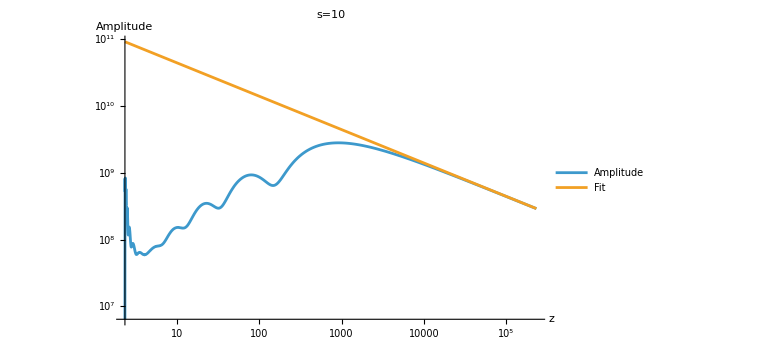

```mathematica
LogLogPlot[{Abs[discZ[expr,10+10^-10 I,z]],Abs[coeff12/Sqrt[z]]},{z,z0t[10],100000z0t[10]},PlotLabel->Style["s=10",16,Bold],AxesLabel->{Style["z",14],Style["Amplitude",14]},PlotLegends->{"Amplitude","Fit"},ImageSize->Large]
```

```mathematica
Clear[It,ItEps,error,tail1,DiscExpr]
tail1[amplitudeT_, s_, J_, d_, start_,a_]:= Module[{zvals, yvals, coeff12},
								zvals = Abs[a start[s]]*{100000,1000000, 10000000};
								yvals=amplitudeT[s,#]&/@zvals;
								coeff12=Mean[yvals*zvals^(1/2)];
								iQInfinity12[10000a start[s], J, d]coeff12]
DiscExpr[s_,z_]:=discZ[expr,s,z]
It[J_,s_,a_]:=MyNIntegrateFaster[DiscExpr[s,z]PolQ[J,6,z],{z,10000a z0t[s],Infinity},16]
ItEps[J_,s_,a_]:=tail1[DiscExpr, s, J, 6, z0t,a]
error[J_,s_,a_]:=Abs[(It[J,s,a]-ItEps[J,s,a])/MyNIntegrateFaster[DiscExpr[s,z]PolQ[J,6,z],{z,2z0t[s],Infinity},16]]
```

```mathematica
N[error[2,5,5]]
```

6.55701×10^-9

```mathematica
TailData2=ParallelTable[{a,error[2,s+10^-9, a]},{s,5,95,10},{a,1,10}];
TailData20=ParallelTable[{a,error[20,s+10^-9, a]},{s,5,95,10},{a,1,10}];
TailData2I=ParallelTable[{a,error[2+I,s+10^-9, a]},{s,5,95,10},{a,1,10}];
```

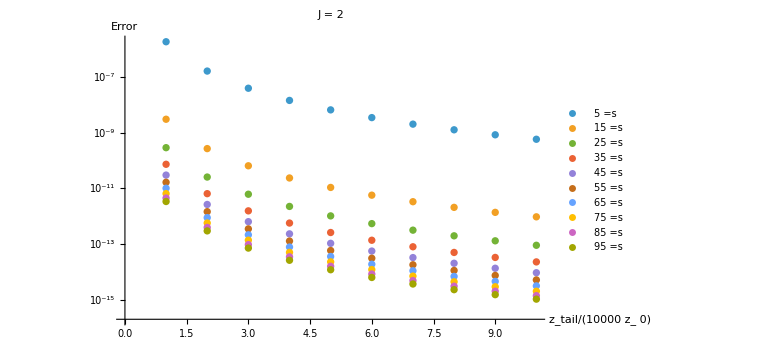

```mathematica
ListLogPlot[TailData2,PlotLabel->Style["J = 2",16,Bold],AxesLabel->{Style[TraditionalForm[HoldForm[z_tail/(10000 z_0)]],14],Style["Error",14]},PlotLegends->"=s"Range[5,95,10],ImageSize->Large]
```

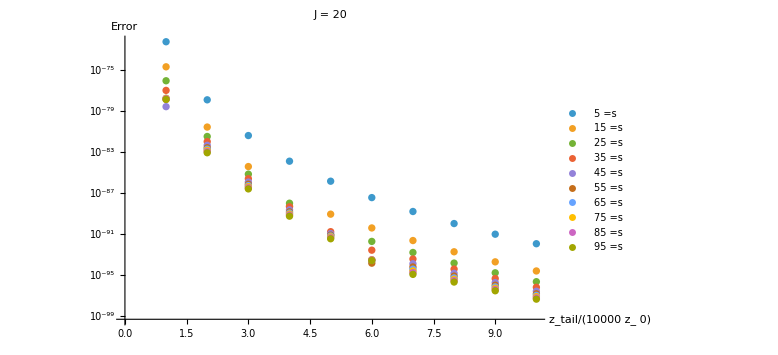

```mathematica
ListLogPlot[TailData20,PlotLabel->Style["J = 20",16,Bold],AxesLabel->{Style[TraditionalForm[HoldForm[z_tail/(10000 z_0)]],14],Style["Error",14]},PlotLegends->"=s"Range[5,95,10],ImageSize->Large]
```

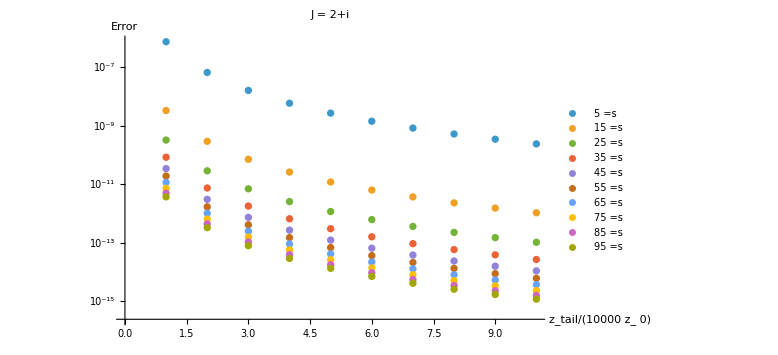

```mathematica
ListLogPlot[TailData2I,PlotLabel->Style["J = 2+i",16,Bold],AxesLabel->{Style[TraditionalForm[
         HoldForm[z_tail/(10000 z_0)]],14],Style["Error",14]},PlotLegends->"=s"Range[5,95,10],ImageSize->Large]
```

## The partial wave plane

#### d = 6 for c_max and Nmax=20

```mathematica
dataAdapt=
```

```mathematica
Clear[sVal]
sVal = Range[5,50,5];
Manipulate[
Clear[data];
data=dataAdapt[[k]];{
ListDensityPlot[data/. {x_,y_,z_}:>{x,y,Log[Abs[z]]},MeshFunctions->{#3&},Mesh->20,PlotLabel->Style[Row[{"s = ",sVal[[k]]}],16, Bold],AxesLabel->{Style["Re(J)",14],Style["Im(J)",14]},PlotLegends->Automatic,ImageSize->Large],
ListDensityPlot[data/. {x_,y_,z_}:>{x,y,Arg[z]},(*MeshFunctions->{#3&},Mesh->15,*)PlotLabel->Row[{"s = ",sVal[[k]]}],PlotLegends->Automatic,ImageSize->Large]},
{k,1,Length[sVal],1}]
```

## Regge trajectories

```mathematica
trajs5to70for6dMaxN20=;
```

```mathematica
cleanTraj[traj_]:=Module[{pairs},pairs=DeleteCases[Partition[traj,2,1],{{_,z_},{_,z_}}];
If[pairs==={},{First[traj]},Prepend[pairs[[All,2]],traj[[1]]]]]
```

```mathematica
allTrajClean=cleanTraj/@Join[trajs5to70for6dMaxN20[[1;;2]],trajs5to70for6dMaxN20[[5;;5]]];
```

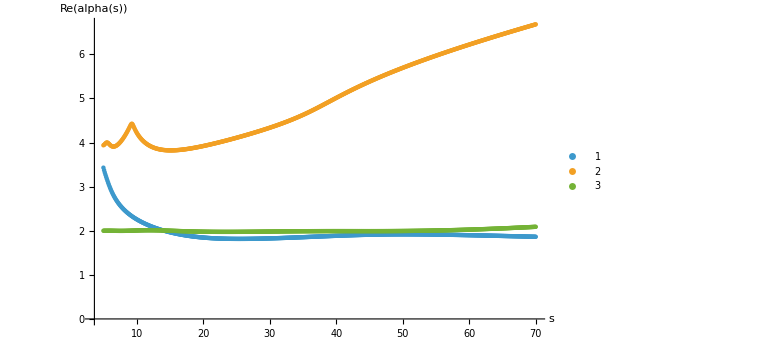

```mathematica
ListPlot[(#[[All]]/. {s_,z_}:>{s,Re[z]})&/@allTrajClean,PlotRange->All, AxesLabel->{"s","Re(alpha(s))"},PlotLegends->Automatic,ImageSize->Large]
```

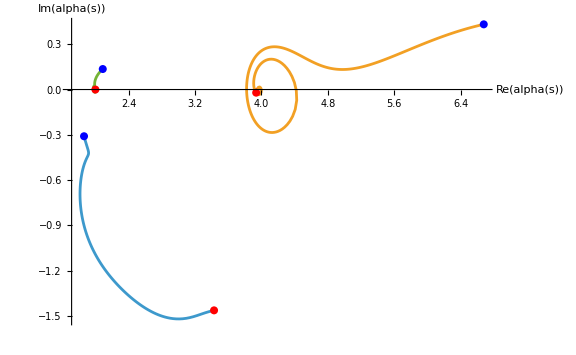

```mathematica
trajPoints=(#[[All]]/. {s_,z_}:>{Re[z],Im[z]})&/@allTrajClean;

starts=First/@trajPoints;
ends=Last/@trajPoints;
ListLinePlot[trajPoints,PlotRange->All,AxesLabel->{"Re(alpha(s))","Im(alpha(s))"},Epilog->{Red,PointSize[0.01],Point[starts],Blue,PointSize[0.01],Point[ends]},ImageSize->Large]
```

## The Veneziano amplitude

```mathematica
Clear[d,kmax, pol]
kmax = 100;
pol =;
```

```mathematica
Clear[polShiftNorm]
polShiftNorm = ParallelTable[pol[[k+1]]/.s->k(z+1)/.d->0//FullSimplify,{k,0,100},Method->"FinestGrained"];
```

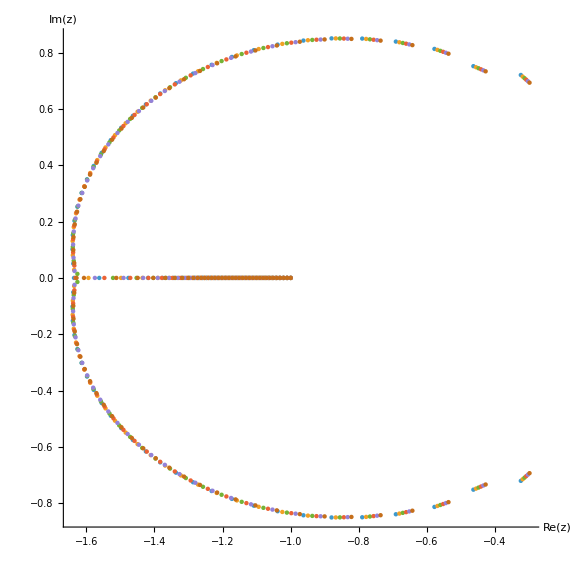

```mathematica
rootsPlot=ComplexListPlot[N[(z/. Solve[#==0,z]&/@polShiftNorm[[90;;100;;2]])],AxesLabel->{"Re(z)","Im(z)"},AspectRatio->1,ImageSize->Large]
```

```mathematica
hatPhi[t_]:=(-√(z^2+y^2 (1+z)^2)-(y (1+(1+k+k z) Coth[y]))/k)*(√(z^2+y^2 (1+z)^2)-(y (1+(1+k+k z) Coth[y]))/k)/.k->100/.z->-1.4+0.64 I/.y->t/2
```

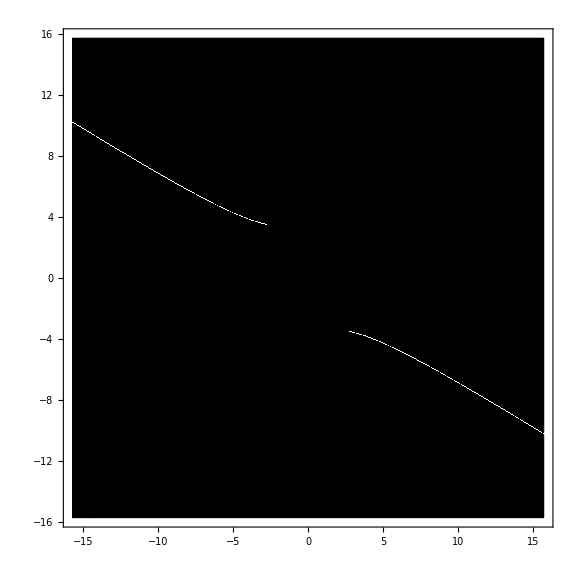

```mathematica
ComplexPlot[hatPhi[z],{z,5Pi(-1-I),5Pi(1+I)},PlotLegends->Automatic,ImageSize->Large]
```

## Toy-model Bessel

```mathematica
kmax=100;
pol = ParallelTable[HypergeometricPFQ[{-n,a+n-1},{},-s/2]//Simplify,{n,0,100}];
```

```mathematica
rootsPlot=ComplexListPlot[N[(s/. Solve[#==0,s]&/@(pol[[80;;100;;2]]/.a->1))](**Table[k,{k,79,99,2}]*),AspectRatio->1]
```